```mathematica
<<peeters` ;
peeters`setGitDir[ "blogit" ]
```

C:\Users\Peeter\cygwin_home\physicsplay\notes\blogit

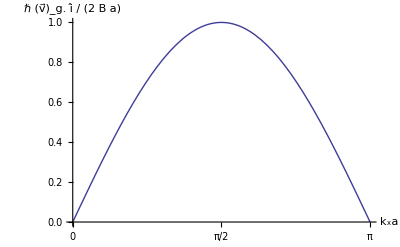

```mathematica
Clear[p]
p = Plot[ Sin[x]
, {x, 0, Pi}
, Ticks -> { {0, Pi/2,Pi}, Automatic }
, AxesLabel->{"k_xa","ℏ (v⃗)_g. î / (2 B a)" }
]
```

```mathematica
peeters`exportForLatex["qmSolidsPs9P2cFig1", p]
```

{C:\Users\Peeter\cygwin_home\physicsplay\notes\blogit/qmSolidsPs9P2cFig1.eps,C:\Users\Peeter\cygwin_home\physicsplay\notes\blogit/qmSolidsPs9P2cFig1pn.png}

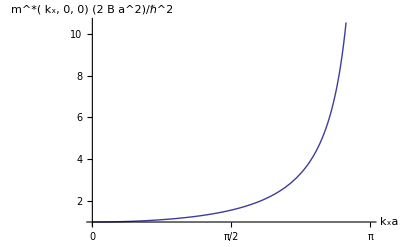

```mathematica
ClearAll[p]
p = Plot[ u/Sin[u]
, {u, 0, Pi}
, Ticks -> {{0, Pi/2, Pi}, Automatic }
, AxesLabel->{ "k_xa","m^*( k_x, 0, 0) (2 B a^2)/ℏ^2" }
(*, PlotRange -> Full*)
]
```

```mathematica
peeters`exportForLatex["qmSolidsPs9P2dFig1", p]
```

{C:\Users\Peeter\cygwin_home\physicsplay\notes\blogit/qmSolidsPs9P2dFig1.eps,C:\Users\Peeter\cygwin_home\physicsplay\notes\blogit/qmSolidsPs9P2dFig1pn.png}

```mathematica
(*Integrate[Sin[x], {x, 0, Pi/2}]*)
```